## Standard Ricker model EWS - vary alpha

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0.01;
bh=0.1;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_alpha";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
(* Realisation number to display *)
displayNum=3;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
```

```mathematica
(* Extract info of one trajectory *)
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
tVals = trajVals[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[trajVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All}];
```

### Plot format adjustment

```mathematica
rTicks=Round[Range[bl,bh,0.02],0.01];
rTicksT=(rTicks-bl)*tmax/(bh-bl);
```

```mathematica
rTicks
```

{0.01,0.03,0.05,0.07,0.09}

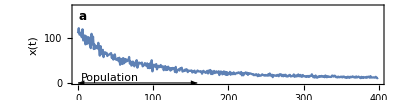

```mathematica
plotTraj=Show[plotX,
PlotRange->{{0,tmax},{0,170}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Density dependence, α"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
]
```

## EWS Plots

### Variance

```mathematica
(* plot colour *)
colVar=TMBcolours[[2]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
varEws//Dimensions
```

{5,400,2}

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[varEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}];
```

### Coefficient of variation

```mathematica
(* plot colour *)
colCV=TMBcolours[[3]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotCv=ListLinePlot[cvEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colCV,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}];
```

### Smax/Mean

```mathematica
(* plot colour *)
colSmaxMean=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Mean"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxMeanEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[smaxMeanEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/<X>",ls],textPos,{-1,0}]}];
```

### Smax/Var

```mathematica
(* plot colour *)
colSmaxVar=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxVar=ListPlot[smaxVarEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/Variance",ls],textPos,{-1,0}]}];
```

### Autocorrelation (combined)

```mathematica
(* plot colour *)
colAC=TMBcolours[[{4,5,7}]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* Construct relevant sub dataframe *)
acEws=Table[Cases[dfEws[[2;;,{1,3,indexEws[[i]]}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims},{i,1,3}];
```

```mathematica
acEws//Dimensions
```

{5,3,400,2}

```mathematica
(* line legend *)
legend=LineLegend[colAC,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotAC=ListLinePlot[acEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
PlotStyle->colAC,
Axes->False,
PlotLegends->Placed[legend,{0.15,0.65}],
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Autocorrelation",ls],textPos,{-1,0}]}];
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

```mathematica
stateVals={"x"};
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.987275 | -0.982296 | -0.982642 | -0.986653 | -0.976418 | -0.981051 | -0.987275 | -0.978354 | -0.986238 | -0.971784 | -0.977524 | -0.979461 | -0.971646 | -0.985961 | -0.987414 | -0.988105 | -0.976418 | -0.986791 | -0.983679 | -0.981604 | -0.971508 | -0.979391 | -0.980705 | -0.974689 | -0.959889 | -0.966736 | -0.980982 | -0.973721 | -0.981397 | -0.988935 | -0.983402 | -0.982711 | -0.979391 | -0.979253 | -0.982988 | -0.978492 | -0.976279 | -0.967773 | -0.98603 | -0.987898 | -0.967358 | -0.973513 | -0.976003 | -0.98444 | -0.98029 | -0.982019 | -0.977732 | -0.986445 | -0.985615 | -0.980429 | -0.979322 | -0.980982 | -0.984025 | -0.986307 | -0.981812 | -0.95083 | -0.978562 | -0.979046 | -0.984025 | -0.964454 | -0.983679 | -0.962241 | -0.966044 | -0.97704 | -0.973721 | -0.98112 | -0.982089 | -0.986791 | -0.984578 | -0.983679 | -0.971715 | -0.980913 | -0.982988 | -0.979115 | -0.964661 | -0.985201 | -0.970194 | -0.979253 | -0.978008 | -0.974965 | -0.97213 | -0.985823 | -0.983126 | -0.985201 | -0.967012 | -0.982158 | -0.97462 | -0.986307 | -0.970747 | -0.978423 | -0.982089 | -0.983887 | -0.98195 | -0.983126 | -0.985408 | -0.986169 | -0.951245 | -0.984302 | -0.989419 | -0.985477

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.399516 | 0.412932 | 0.547994 | 0.0071231 | 0.245574 | 0.439142 | 0.692185 | 0.175726 | 0.395021 | 0.282988 | 0.421853 | -0.256916 | 0.460788 | 0.136929 | 0.00138313 | 0.580014 | 0.27787 | 0.417911 | -0.0901798 | 0.482158 | 0.152974 | 0.684716 | 0.0150761 | 0.676902 | 0.418465 | 0.0168741 | 0.171093 | 0.257815 | 0.392254 | 0.22621 | 0.247095 | 0.417704 | -0.00159059 | 0.46964 | 0.610373 | 0.321853 | 0.384855 | 0.650968 | 0.0995851 | 0.182918 | 0.386722 | 0.38852 | -0.183057 | 0.785685 | -0.0345781 | 0.168949 | 0.231881 | 0.586307 | -0.136999 | 0.466321 | -0.186376 | 0.203527 | 0.188658 | 0.435408 | 0.0109959 | 0.173997 | 0.393223 | 0.631051 | -0.529945 | 0.673375 | 0.36556 | 0.609198 | 0.644467 | 0.262794 | 0.679184 | 0.0674965 | 0.383126 | -0.127524 | -0.0937068 | 0.347718 | 0.1287 | 0.232573 | 0.584163 | 0.672337 | 0.350346 | 0.577801 | 0.557607 | 0.544882 | 0.0573306 | 0.43195 | 0.18361 | 0.283887 | 0.321438 | 0.387759 | 0.443568 | -0.0681189 | 0.480844 | 0.6713 | 0.381743 | 0.377109 | 0.366044 | 0.18444 | 0.40249 | 0.292116 | 0.475035 | 0.597026 | 0.0647994 | 0.191701 | 0.567981 | -0.602974

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxMean,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.74343 | -0.564385 | -0.635339 | -0.882365 | -0.622752 | -0.153112 | -0.622199 | -0.101798 | 0.0709544 | 0.151936 | -0.728492 | 0.606293 | -0.529461 | -0.0829184 | -0.604772 | -0.715353 | 0.569156 | -0.566459 | -0.0235131 | -0.655394 | -0.358506 | -0.428354 | -0.711411 | -0.340733 | -0.509889 | -0.312517 | -0.172407 | -0.366874 | -0.0692946 | -0.57953 | -0.130636 | -0.596611 | -0.282849 | -0.547649 | 0.0618257 | -0.343568 | -0.464039 | -0.27538 | -0.167773 | -0.551314 | -0.723928 | -0.563001 | -0.0511757 | -0.340802 | -0.151729 | -0.490249 | 0.282988 | -0.464592 | -0.0419779 | -0.543015 | -0.0293223 | 0.290041 | -0.170816 | -0.785685 | 0.737206 | -0.329046 | -0.124827 | -0.545989 | -0.448133 | -0.0583679 | -0.242324 | -0.222407 | -0.131881 | -0.133817 | -0.515906 | -0.117911 | -0.583472 | 0.111411 | -0.285961 | -0.640871 | -0.37538 | -0.0771784 | -0.295643 | -0.31556 | -0.512241 | -0.691978 | -0.507192 | -0.0223375 | 0.168396 | -0.20166 | -0.489142 | -0.243084 | -0.228631 | -0.208091 | -0.362656 | -0.492531 | -0.116943 | -0.464039 | -0.379737 | -0.0309129 | -0.321646 | -0.323444 | -0.12296 | -0.649447 | -0.654011 | -0.599447 | 0.42047 | -0.114454 | -0.818465 | -0.665975

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colCV,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.873333 | -0.92 | -0.92 | -0.913333 | -0.886667 | -0.893333 | -0.94 | -0.906667 | -0.88 | -0.806667 | -0.913333 | -0.926667 | -0.866667 | -0.873333 | -0.873333 | -0.933333 | -0.886667 | -0.96 | -0.946667 | -0.893333 | -0.913333 | -0.88 | -0.88 | -0.893333 | -0.786667 | -0.866667 | -0.906667 | -0.953333 | -0.846667 | -0.893333 | -0.913333 | -0.893333 | -0.913333 | -0.8 | -0.893333 | -0.886667 | -0.913333 | -0.9 | -0.973333 | -0.806667 | -0.906667 | -0.92 | -0.78 | -0.906667 | -0.873333 | -0.9 | -0.613333 | -0.886667 | -0.92 | -0.88 | -0.84 | -0.88 | -0.94 | -0.88 | -0.88 | -0.873333 | -0.88 | -0.92 | -0.953333 | -0.926667 | -0.906667 | -0.853333 | -0.846667 | -0.853333 | -0.893333 | -0.813333 | -0.953333 | -0.946667 | -0.926667 | -0.893333 | -0.933333 | -0.9 | -0.846667 | -0.886667 | -0.893333 | -0.9 | -0.886667 | -0.873333 | -0.9 | -0.933333 | -0.926667 | -0.946667 | -0.906667 | -0.94 | -0.746667 | -0.926667 | -0.92 | -0.906667 | -0.92 | -0.933333 | -0.913333 | -0.913333 | -0.933333 | -0.886667 | -0.92 | -0.9 | -0.846667 | -0.886667 | -0.94 | -0.926667

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxMean,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.133333 | 0.12 | -0.366667 | -0.0533333 | 0.166667 | 0.4 | 0.32 | 0.353333 | 0.526667 | 0.486667 | 0.266667 | -0.0533333 | -0.233333 | 0.206667 | 0.446667 | -0.206667 | 0.413333 | 0.206667 | -0.153333 | 0.44 | 0.233333 | 0.24 | 0.6 | 0.58 | 0.506667 | 0.746667 | 0.0866667 | 0.16 | 0.08 | 0.726667 | 0.24 | 0.486667 | 0.12 | 0.02 | 0.2 | 0.493333 | -0.00666667 | 0.206667 | -0.133333 | 0.6 | 0.02 | 0.08 | 0.78 | -0.0666667 | 0.38 | 0.16 | 0.513333 | 0.546667 | -0.08 | 0.166667 | 0.286667 | 0.32 | 0.34 | 0.0733333 | 0.68 | 0.34 | 0.433333 | 0.213333 | -0.26 | 0.326667 | 0.1 | -0.133333 | 0.373333 | 0.753333 | 0.18 | 0.48 | -0.126667 | 0.04 | 0.166667 | 0.02 | 0.04 | 0.0133333 | 0.34 | -0.293333 | 0.46 | 0.353333 | 0.34 | 0.413333 | 0.366667 | 0.313333 | 0.38 | 0.666667 | 0.453333 | 0.673333 | 0.353333 | 0.24 | 0.44 | -0.346667 | 0.14 | 0.113333 | 0.58 | 0.193333 | -0.02 | 0.08 | -0.226667 | 0.1 | 0.346667 | 0.473333 | 0.333333 | 0.346667

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colSmaxVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

### Lag-1 Autocorrelation

```mathematica
indexKtau1=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]];
indexKtau2=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]];
indexKtau3=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ktauVals1=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau1}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals2=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau2}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals3=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau3}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[{ktauVals1[[;;,2;;]][[1]],ktauVals2[[;;,2;;]][[1]],ktauVals3[[;;,2;;]][[1]]},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colAC,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

## Power Spectrum Plot

### Colour function

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[10;;;;4]]
```

{249.,289.,329.,369.}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,_,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
specData//Dimensions
```

{4,41,2}

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,7}]],{displayNum,"x",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
timeRange
```

{249.,369.}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(309-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->{-2,10},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,10,2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

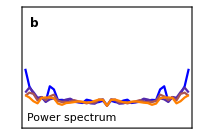

```mathematica
(* normalised power spectrum plot *)
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.2,1},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,1,0.2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

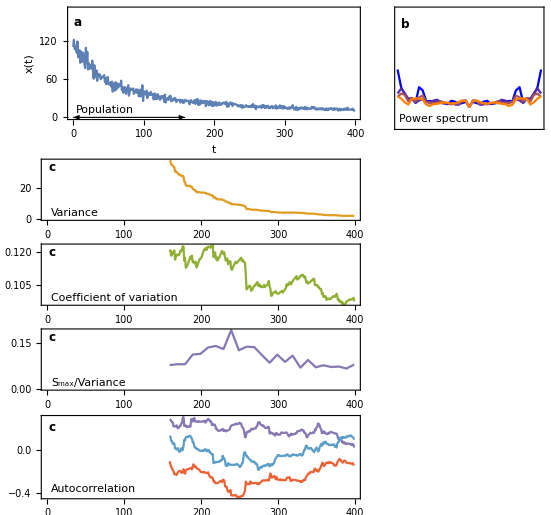

```mathematica
plotGrid
```

```mathematica
Export["figures/single_"<>simName<>".png",plotGrid,ImageResolution->200];
```